## Author Informations

#### Authors: A. C. Lehum, Huan Souza Date: 18/05/2021 Filiation: Universidade Federal do Pará Emails: lehum@ufpa.br, huan.souza@icen.ufpa.br

# Electrodynamics coupled to linearized gravity

#### Preliminaries

```mathematica
Quit[]
```

```mathematica
description="Electrodynamics coupled to linearized gravity";
If[$FrontEnd===Null,$FeynCalcStartupMessages=False;
Print[description];];
If[$Notebooks===False,$FeynCalcStartupMessages=False];
$LoadAddOns={"FeynArts","FeynHelpers"};
Get["FeynCalc`"]
$FAVerbose=0;
FCCheckVersion[9,3,0];
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (3 Aug 2020) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
FAPatch[PatchModelsOnly->True];
$KeepLogDivergentScalelessIntegrals=True;
MakeBoxes[mu,TraditionalForm]:="μ";
MakeBoxes[nu,TraditionalForm]:="ν";
MakeBoxes[p1,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(1\)]\)";
MakeBoxes[p2,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(2\)]\)";
MakeBoxes[p3,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(3\)]\)";
MakeBoxes[p4,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(4\)]\)";
MakeBoxes[k1,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(1\)]\)";
MakeBoxes[k2,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(2\)]\)";
MakeBoxes[k3,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(3\)]\)";
MakeBoxes[k4,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(4\)]\)";
MakeBoxes[m1,TraditionalForm]:="\!\(\*SubscriptBox[\(m\), \(1\)]\)";
MakeBoxes[m2,TraditionalForm]:="\!\(\*SubscriptBox[\(m\), \(2\)]\)";
ScalarProduct[p,p]=p^2
```

p^2

#### 1-loop γ self-energy

```mathematica
fields1={InsertionLevel->{Classes},GenericModel->FileNameJoin[{"Einstein_QED_2","Einstein_QED_2"}],Model->FileNameJoin[{"Einstein_QED_2","Einstein_QED_2"}]};
top1[i_,j_]:=CreateTopologies[1,i->j,ExcludeTopologies->{Reducible},Adjacencies->{3,4}];
seph1=(InsertFields[#1,{V[1]}->{V[1]},Sequence@@fields1]&)[top1[1,1]];
```

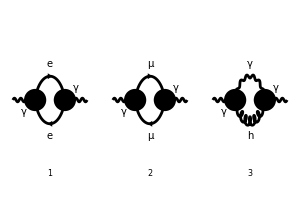

```mathematica
Paint[seph1,ColumnsXRows->{3,2},SheetHeader->{"Photon self-energy"},Numbering->Simple,ImageSize->{300,200}];
```

```mathematica
AbsoluteTiming[For[
i=1,i≤3,i++,{
Pamp[i]=DiagramExtract[seph1,i],
Pamp1[i]=FCFAConvert[CreateFeynAmp[Pamp[i],Truncated->True],IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{k},List->False,SMP->True,ChangeDimension->D,LorentzIndexNames->{mu,nu,α,γ,δ,β,ξ,χ},UndoChiralSplittings->True]//DotExpand//Simplify//Expand,
Pamp2[i]=TID[Pamp1[i],k,ToPaVe->True]//DiracSimplify//Simplify,
Pamp3[i]=PaXEvaluate[Pamp2[i],$FCAdvice=False],
Pamp4[i]=Coefficient[Pamp3[i],1/Epsilon]*1/Epsilon//Expand//Factor}
];]
```

{4.33709,Null}

```mathematica
photon[1]=Sum[Pamp4[i],{i,1,3}]//DotExpand//Simplify//Expand//Factor
```

-((16 e^2+κ^2 p^2) (p^2 g^μν-p^μ p^ν))/(96 π^2 ε)

#### 1-loop electron self-energy

```mathematica
fields1={InsertionLevel->{Classes},GenericModel->FileNameJoin[{"Einstein_QED_2","Einstein_QED_2"}],Model->FileNameJoin[{"Einstein_QED_2","Einstein_QED_2"}]};
top1[i_,j_]:=CreateTopologies[1,i->j,ExcludeTopologies->{Reducible},Adjacencies->{3,4}];
sepsi1=(InsertFields[#1,{F[1]}->{F[1]},Sequence@@fields1]&)[top1[1,1]];
```

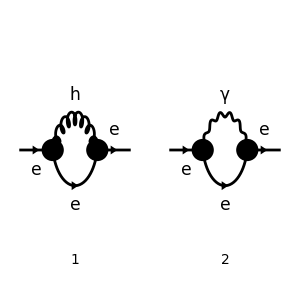

```mathematica
Paint[sepsi1,ColumnsXRows->{2,1},SheetHeader->{"Electron self-energy"},Numbering->Simple,ImageSize->{300,300}];
```

```mathematica
AbsoluteTiming[For[
i=1,i≤2,i++,{
Famp[i]=DiagramExtract[sepsi1,i],
Famp1[i]=FCFAConvert[CreateFeynAmp[Famp[i],Truncated->True],IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{k},List->False,SMP->True,ChangeDimension->D,LorentzIndexNames->{mu,nu,α,γ,δ,β,ξ,χ},UndoChiralSplittings->True]//DotExpand//Simplify//Expand,
Famp2[i]=TID[Famp1[i],k,ToPaVe->True]//DiracSimplify//Simplify,
Famp3[i]=PaXEvaluate[Famp2[i],$FCAdvice=False],
Famp4[i]=Coefficient[Famp3[i],1/Epsilon]*1/Epsilon//Expand//Factor}
];]
```

{2.25371,Null}

```mathematica
fermion[1]=Sum[Famp4[i],{i,1,2}]//DotExpand//Simplify//Expand//Factor
```

-(-8 e^2 γ·p+32 e^2 m_1+κ^2 p^2 γ·p-3 κ^2 p^2 m_1-2 κ^2 m_1^2 γ·p+2 κ^2 m_1^3)/(128 π^2 ε)

```mathematica
fermionHO[1]=Coefficient[fermion[1],p^2]*p^2//Simplify//Expand//Simplify
```

(κ^2 p^2 (3 m_1-γ·p))/(128 π^2 ε)

The divergence fermionHO[1] is absorbed by a high order counterterm.

```mathematica
fermionDirac[1]=fermion[1]/.{p^2->0}//Simplify//Expand//Simplify
```

((4 e^2+κ^2 m_1^2) γ·p-m_1 (16 e^2+κ^2 m_1^2))/(64 π^2 ε)

The term fermionDirac[1] is the UV divergent correction to Dirac Lagrangian.  The muon self-energy is obtained by the replacement of F[1]  to F[2] in the sepsi1 function.

#### 1-loop vertex correction

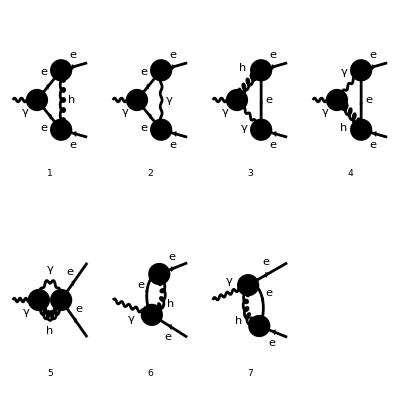

```mathematica
fields1={InsertionLevel->{Classes},GenericModel->FileNameJoin[{"Einstein_QED_2","Einstein_QED_2"}],Model->FileNameJoin[{"Einstein_QED_2","Einstein_QED_2"}]};
top1[i_,j_]:=CreateTopologies[1,i->j,ExcludeTopologies->{Reducible},Adjacencies->{3,4,5}];
vertex1=(InsertFields[#1,{V[1]}->{F[1],-F[1]},Sequence@@fields1]&)[top1[1,2]];
Paint[vertex1,ColumnsXRows->{4,2},SheetHeader->{"Vertex correction"},Numbering->Simple,ImageSize->{400,400}];
```

```mathematica
AbsoluteTiming[For[
i=1,i≤7,i++,{
amp[i]=DiagramExtract[vertex1,i],
amp1[i]=FCFAConvert[CreateFeynAmp[amp[i],Truncated->True],IncomingMomenta->{p},OutgoingMomenta->{q,l},LoopMomenta->{k},List->False,SMP->True,ChangeDimension->D,LorentzIndexNames->{mu,nu,α,γ,δ,β,ξ,χ},UndoChiralSplittings->True]//DotExpand//Simplify//Expand,
amp2[i]=TID[amp1[i],k,ToPaVe->True]//DiracSimplify//Simplify,
amp3[i]=PaXEvaluate[amp2[i],$FCAdvice=False],
amp4[i]=Coefficient[amp3[i],1/Epsilon]*1/Epsilon//Expand//Factor}
];]
```

{4699.52,Null}

This computation takes a long time (~78 minutes on M1 MacBook Air), so we turn the results available for upload:

```mathematica
SetDirectory["Your directory with results here"]
```

In my case,

```mathematica
SetDirectory["/Users/lehum/Desktop/Einstein-QED - 2/results"]
```

/Users/lehum/Desktop/Einstein-QED - 2/results

```mathematica
amp4[1]=<<amp41.m;
amp4[2]=<<amp42.m;
amp4[3]=<<amp43.m;
amp4[4]=<<amp44.m;
amp4[5]=<<amp45.m;
amp4[6]=<<amp46.m;
amp4[7]=<<amp47.m;
```

```mathematica
vertex1l[1]=Sum[amp4[i],{i,1,7}]//DotExpand//Simplify//Expand
```

-(γ^μ e^3)/(16 ε π^2)-(κ^2 m_1^2 γ^μ e)/(64 ε π^2)+(27 κ^2 m_1 γ^μ.(γ·l) e)/(1024 ε π^2)-(3 κ^2 m_1 γ^μ.(γ·p) e)/(256 ε π^2)-(3 κ^2 m_1 γ^μ.(γ·q) e)/(512 ε π^2)+(3 κ^2 m_1 (γ·l).γ^μ e)/(1024 ε π^2)+(3 κ^2 m_1 (γ·p).γ^μ e)/(256 ε π^2)-(15 κ^2 m_1 (γ·q).γ^μ e)/(512 ε π^2)-(3 κ^2 m_1 γ^μ.(γ·l).(γ̄)^6 e)/(128 ε π^2)-(3 κ^2 m_1 γ^μ.(γ·l).(γ̄)^7 e)/(128 ε π^2)+(κ^2 γ^μ.(γ·l).(γ·p) e)/(128 ε π^2)+(κ^2 γ^μ.(γ·l).(γ·q) e)/(256 ε π^2)-(κ^2 γ^μ.(γ·p).(γ·l) e)/(512 ε π^2)+(κ^2 γ^μ.(γ·p).(γ·q) e)/(256 ε π^2)+(5 κ^2 γ^μ.(γ·q).(γ·l) e)/(1024 ε π^2)-(κ^2 γ^μ.(γ·q).(γ·p) e)/(128 ε π^2)-(κ^2 (γ·l).γ^μ.(γ·p) e)/(256 ε π^2)+(11 κ^2 (γ·l).γ^μ.(γ·q) e)/(1024 ε π^2)+(κ^2 (γ·l).(γ·p).γ^μ e)/(256 ε π^2)+(κ^2 (γ·l).(γ·q).γ^μ e)/(512 ε π^2)+(κ^2 (γ·p).γ^μ.(γ·l) e)/(512 ε π^2)-(κ^2 (γ·p).γ^μ.(γ·q) e)/(256 ε π^2)-(κ^2 (γ·p).(γ·l).γ^μ e)/(128 ε π^2)+(κ^2 (γ·p).(γ·q).γ^μ e)/(128 ε π^2)+(3 κ^2 m_1 (γ·q).γ^μ.(γ̄)^6 e)/(128 ε π^2)+(3 κ^2 m_1 (γ·q).γ^μ.(γ̄)^7 e)/(128 ε π^2)-(5 κ^2 (γ·q).γ^μ.(γ·l) e)/(1024 ε π^2)+(κ^2 (γ·q).γ^μ.(γ·p) e)/(512 ε π^2)+(κ^2 (γ·q).(γ·l).γ^μ e)/(1024 ε π^2)-(κ^2 (γ·q).(γ·p).γ^μ e)/(512 ε π^2)+(κ^2 γ·l l^μ e)/(96 ε π^2)+(κ^2 γ·p l^μ e)/(64 ε π^2)-(κ^2 γ·q l^μ e)/(768 ε π^2)+(9 κ^2 m_1 l^μ e)/(512 ε π^2)-(κ^2 γ·l q^μ e)/(192 ε π^2)+(κ^2 γ·p q^μ e)/(64 ε π^2)+(κ^2 γ·q q^μ e)/(96 ε π^2)-(3 κ^2 m_1 q^μ e)/(256 ε π^2)-(11 κ^2 γ^μ l^2 e)/(768 ε π^2)+(3 κ^2 γ^μ.(γ̄)^6 l^2 e)/(256 ε π^2)+(3 κ^2 γ^μ.(γ̄)^7 l^2 e)/(256 ε π^2)-(κ^2 γ^μ (l·p) e)/(64 ε π^2)-(29 κ^2 γ^μ (l·q) e)/(1536 ε π^2)-(κ^2 γ^μ (p·q) e)/(64 ε π^2)-(11 κ^2 γ^μ q^2 e)/(768 ε π^2)+(3 κ^2 γ^μ.(γ̄)^6 q^2 e)/(256 ε π^2)+(3 κ^2 γ^μ.(γ̄)^7 q^2 e)/(256 ε π^2)

```mathematica
vertex1l[2]=vertex1l[1]/.{Momentum[l,D]->0,Momentum[p,D]->0,Momentum[q,D]->0}//DotExpand//Simplify//Factor//Expand
```

-(e^3 γ^μ)/(16 π^2 ε)-(e κ^2 m_1^2 γ^μ)/(64 π^2 ε)

where vertex1l[2] is the UV divergent part of the vertex1 amplitude that is absorbed by the counterterm Z_1. All UV divergences depending on external momenta will be absorbed by high order counterterms. 
In addition, the vertex interaction involving muons is obtained by the replacement of F[1] to F[2] in the vertex1 function.